## Дунаев Виктор , 3 курс , 6 группа , Вариант 23

## Task 1

```mathematica
vertex = {1,2,3,4,5,6};
```

```mathematica
edges = {1->5,2->5,3->1,3->4,3->5,4->1,4->2,4->6,5->4,6->2,6->3,6->5};
```

## Task 2

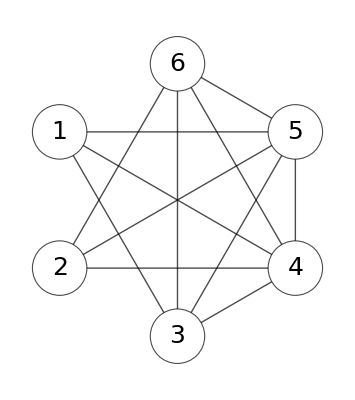

```mathematica
MYgraffon = Graph[vertex,edges, VertexSize->Large, VertexStyle->White, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Italic,25], GraphLayout->{"CircularEmbedding"},EdgeShapeFunction->"Arrow", EdgeStyle->Black]
```

## Task 3

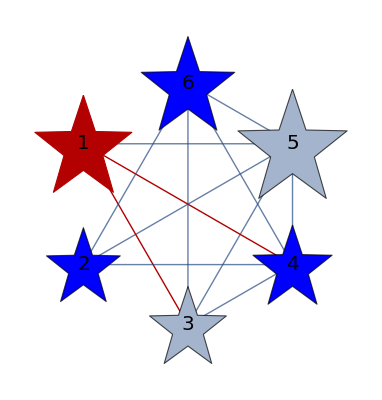
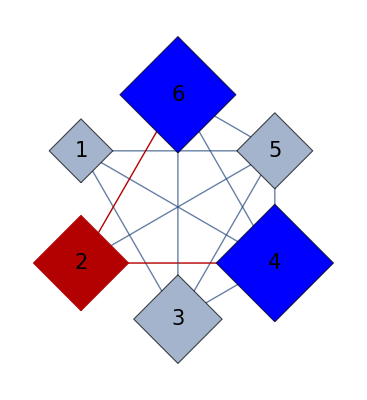
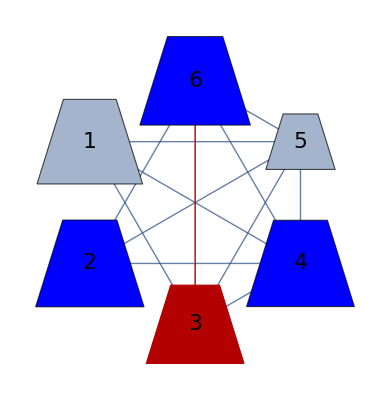
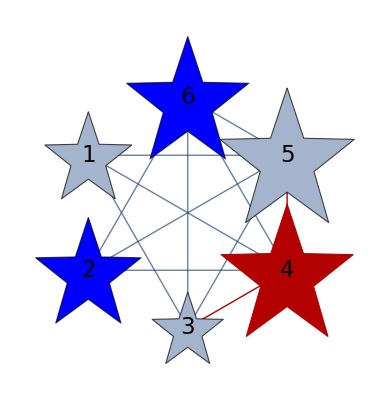
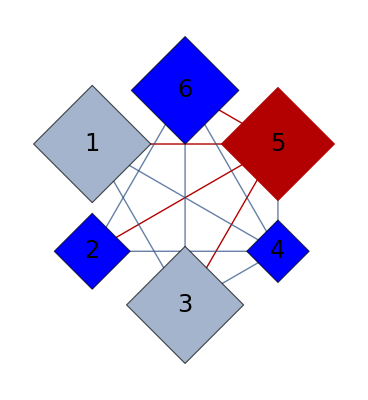
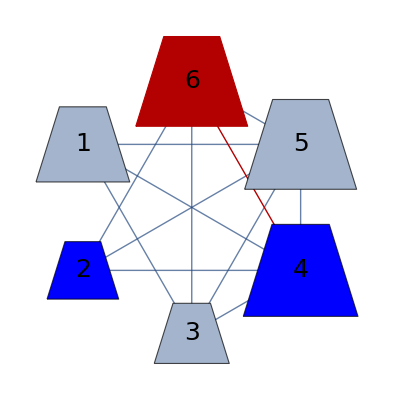

```mathematica
Table[Graph[vertex,edges, VertexSize->Table[i->RandomReal[{0.5,1}],{i,1,6}],VertexShapeFunction-> {"UpTrapezoid", "Star", "Diamond"}⟦Mod[k,3]+1⟧,VertexStyle->{_?EvenQ->Blue}, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Italic,19+k],GraphHighlight->{k,_->k}, GraphLayout->{"CircularEmbedding"}],{k,1,6}]
```

## Task 4

```mathematica
getMyGraph[vertexNum_,edgesNum_]:=(
ClearAll[edges,vertex];
vertex = Table[i,{i,1,vertexNum}];
edges = Table[i->#&/@RandomChoice[vertex,edgesNum],{i,1,vertexNum}];
edges = RandomChoice[Flatten[edges],edgesNum];
Graph[vertex,edges]
)
```

```mathematica
getMyGraph[6,15]
```

-Graphics-

## Task 5

## Sad Smile : (